```mathematica
Clear["Global`*"]
```

```mathematica
c=3*10^8;(*spd of light*)
```

### Gaussian pulse parameters

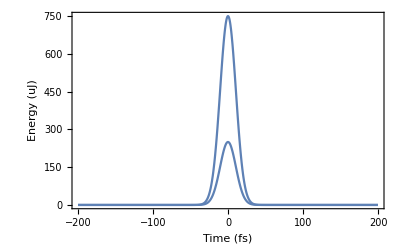

```mathematica
energy={.25,.75}*10^-3;(*total energy of pulse in J*)
tp=35*10^-15;(*pulse duration in s, FWHM of intensity profile as a function of time*)
P=energy/tp;(*total power of pulse in W, this is actually peak power?*)
field[t_]=√P*Exp[-4*Log[2] t^2/tp^2];(*field we use for NLSE according to papers*)
Plot[field[t*10^-15]^2*tp*10^6,{t,-200,200},Frame->True,FrameLabel->{"Time (fs)","Energy (uJ)"},PlotRange->All]
```

### Pulse in frequency space

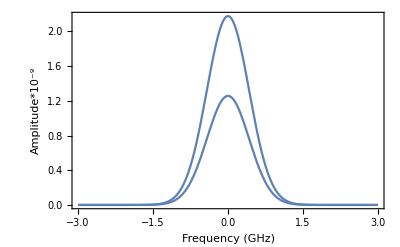

```mathematica
ft[w_]=FourierTransform[field[t],t,w];
Plot[ft[(w*10^15)/(2π)]*10^9,{w,-3,3},Frame->True,FrameLabel->{"Frequency (GHz)","Amplitude*10^-9"},PlotRange->All]
```

#### Spectral width

```mathematica
specFWHMw=2*NSolve[ft[w]==ft[0]/2,w][[2,1,2]](*in rad*Hz*)
specFWHMf=specFWHMw/(2π);
((780*10^-9)^2)/c*specFWHMf*10^9
((390*10^-9)^2)/c*specFWHMf*10^9
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

1.58434×10^14

51.137

12.7843